## Hexi—PS4—2025 - 02-04

### Exercises from EIWL3 Section 14

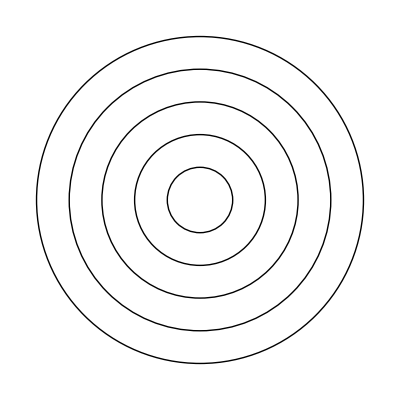

```mathematica
Graphics[Table[Circle[{0,0},r],{r,1,5}]]
```

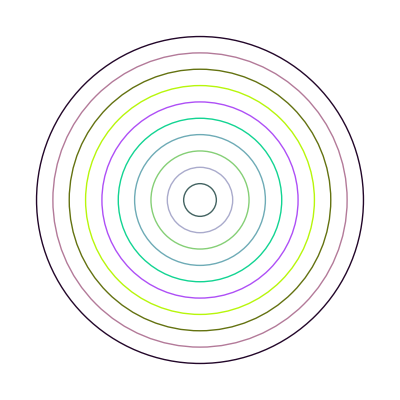

```mathematica
Graphics[Table[Style[Circle[{0,0},r],RandomColor[]],{r,1,10,1}]]
```

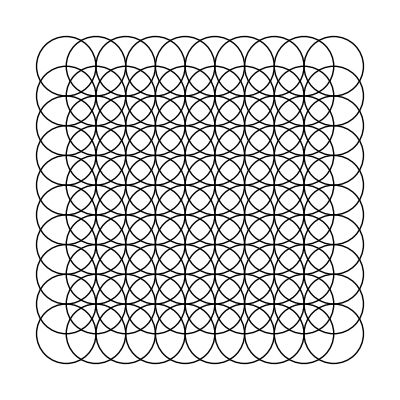

```mathematica
Graphics[Table[Circle[{x,y}],{x,0,9},{y,0,9}]]
```

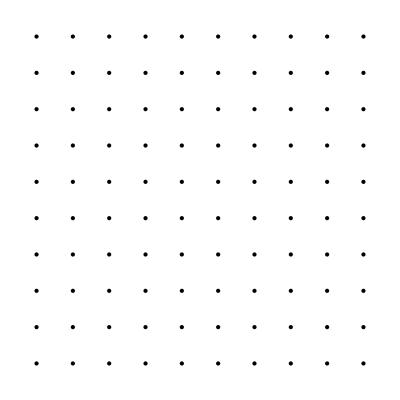

```mathematica
Graphics[Table[Point[{x,y}],{x,10},{y,10}]]
```

```mathematica
Manipulate[Graphics[Table[Circle[{0,0},r],{r,1,x}]],{x,1,20,1}]
```

```mathematica
Graphics3D[Table[Style[Sphere[RandomInteger[10,3]],RandomColor[]],50]]
```

-Graphics3D-

```mathematica
Graphics3D[Table[Style[Sphere[{x,y,z},1/2],RGBColor[x/11,y/11,z/11]],{x,11},{y,11},{z,11}]]
```

-Graphics3D-

```mathematica
Manipulate[Graphics[Table[Circle[{t*x,0},x],{x,1,10}]],{t,-2,2}]
```

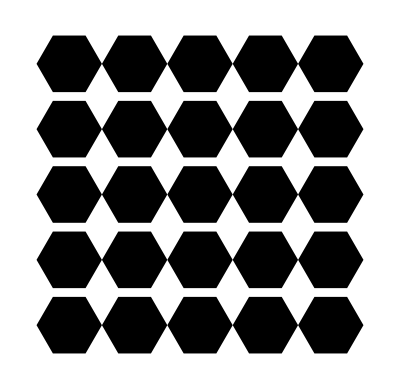

```mathematica
Graphics[Table[RegularPolygon[{x,y},1/2,6],{x,1,5},{y,1,5}]]
```

```mathematica
Graphics3D[Line[{Table[{RandomInteger[50],RandomInteger[50],RandomInteger[50]},50]}]]
```

-Graphics3D-

```mathematica
Manipulate[Graphics3D[Style[{Icosahedron[{0,0,0},s],Dodecahedron[{0,0,0},1]},Opacity[0.5]]],{s,1,2}]
```

### Exercises from EIWL3 Section 14

```mathematica
UnitConvert[Quantity[4.5, "Pounds"],"Kilograms"]
```

2.04117 kg

```mathematica
UnitConvert[Quantity[60.25, ("Miles")/("Hours")],"Kilometers per hour"]
```

96.963 km/h

```mathematica
UnitConvert[Entity["Building","EiffelTower::5h9w8"][EntityProperty["Building","Height"]],"Miles"]
```

0.205052 mi

```mathematica
Entity["Mountain","MountEverest"][EntityProperty["Mountain","Elevation"]]/Entity["Building","EiffelTower::5h9w8"][EntityProperty["Building","Height"]]
```

26.8147

```mathematica
Entity["Planet","Earth"][EntityProperty["Planet","Mass"]]/Entity["PlanetaryMoon","Moon"][EntityProperty["PlanetaryMoon","Mass"]]
```

81.3

```mathematica
CurrencyConvert[Quantity[2500., "Yen"],Quantity[, "USDollars"]]
```

16.14 $

```mathematica
UnitConvert[35 Quantity[, "Ounces"]+Quantity[0.25, "ShortTons"]+45 Quantity[, "Pounds"]+9 Quantity[, "Stones"],"Kilograms"]
```

305.353 kg

```mathematica
UnitConvert[EntityValue[EntityClass["Planet",All],"DistanceFromEarth"],"Light minutes"]
```

{11.7365 light minutes,4.22104 light minutes,0. light minutes,5.76336 light minutes,38.0317 light minutes,86.7436 light minutes,161.122 light minutes,254.493 light minutes}

```mathematica
Rotate["hello",180Degree]
```

hello

```mathematica
Table[Rotate[Style["A",100],x Degree],{x,0,360,30}]
```

{A,A,A,A,A,A,A,A,A,A,A,A,A}

```mathematica
Manipulate[Rotate[Entity["TaxonomicSpecies","FelisCatus::ddvt3"]["Image"],x Degree],{x,0,180}]
```

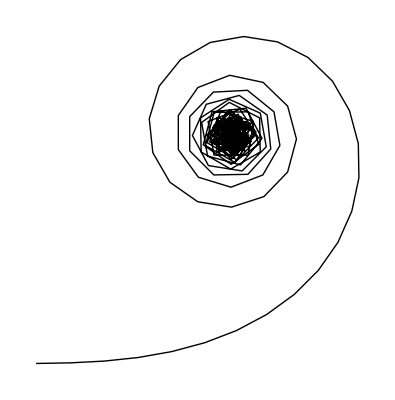

```mathematica
Graphics[Line[AnglePath[Range[180]Degree]]]
```

```mathematica
Manipulate[Graphics[Line[AnglePath[Table[x Degree,100]]]],{x,0,360}]
```

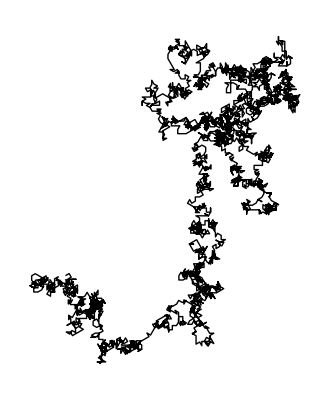

```mathematica
Graphics[Line[AnglePath[IntegerDigits[2^10000]*30 Degree]]]
```